# Q4

2

25

{{-2,-2},{-1,-2},{1,-2},{2,-2},{-2,-1},{2,-1},{-2,1},{2,1},{-2,2},{-1,2},{1,2},{2,2}}

{{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{0,1},{1,1}}

{{0,-2},{-2,0},{2,0},{0,2}}

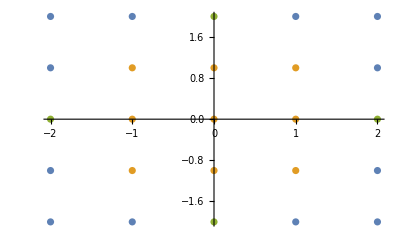

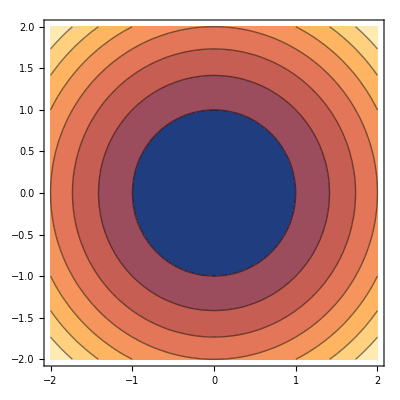

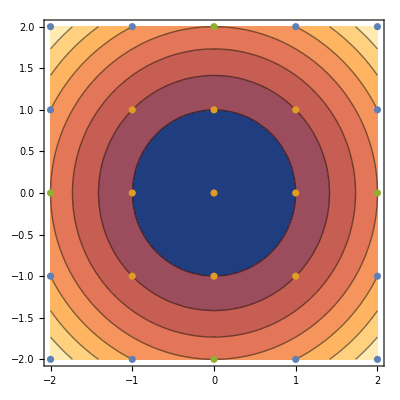

```mathematica
(*i*)
c=Input[]
(*ii*)
f[x_,y_]:=x^2+y^2-c^2
out={};
in={};
on={};
Do[
Do[
 If[f[x,y]==0,
AppendTo[on,{x,y}],
If[f[x,y]<0,
AppendTo[in,{x,y}],
If[f[x,y]>0,
AppendTo[out,{x,y}]
]
]
]
,{x,-c,c}]
,{y,-c,c}
];
Length[in]+Length[out]+Length[on]
out
in
on
p1 =ListPlot[{out,in,on}];
t1=ContourPlot[f[x,y],{x,-c,c},{y,-c,c}];
Show[t1,p1]
```